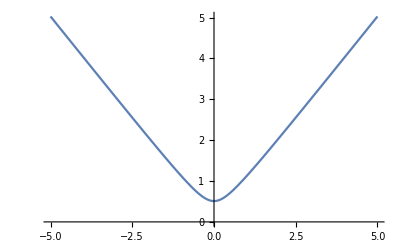

d e / d n == mu   OK

electron pressure at mu=4MeV is: 2.0591 MeV^4

d p / d mu == n   OK

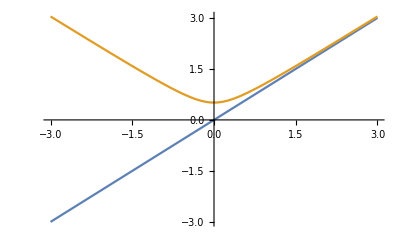

Ultrarelativistic limit of pressure OK

Nonrelativistic limit of energy density OK

Nonrelativistic d p / d mu == n   OK

```mathematica
(*Physics 584,Computational Methods,Mark Alford,March 2016 Exercise 1:Free fermion gas at zero temperature*)e$1[p_,m_]=Module[{},Sqrt[p^2 + m^2] (*fill in single particle dispersion relation here*)];
Plot[e$1[p,0.51],{p,-5,+5}]
(*Make a plot of the dispersion relation of electrons (mass=0.51 MeV) for momenta from-5 MeV to+5 MeV*)

number$density[pF_,m_]=Module[{},pF^3/(3*Pi^2)];

energy$density[pF_,m_]=Module[{}, 1/π^2 Integrate[e$1[p,m] p^2,{p,0,pF},Assumptions->{m>0 ,pF>0,e}](*to be filled in using e$1[p,m]*)(*note that you may need to use the "Assumptions" option to help mathematica to evaluate the integral*)];

(*Physical value of Fermi momentum for a given chemical potential:*)
pFermi[mu_,m_]=Module[{},Sqrt[mu^2-m^2](*to be filled in*)];

(*Test that for the physical value of the Fermi momentum,d e/d n is mu:*)
If[FullSimplify[D[energy$density[pF,m],pF]/D[number$density[pF,m],pF]]== e$1[pF,m](*fill in code for the condition de/dn==mu.You will need to use Simplify[] and tell it that mu>m and m>0*)
,Print["d e / d n == mu   OK"],(*else*)Print["**** d e / d n == mu failed"]];

pressure[mu_,m_]=Module[{pF=pFermi[mu,m]},FullSimplify[mu number$density[pF,m]-energy$density[pF,m]](*fill this in*)];

(*Evaluate the pressure in MeV^4 of a gas of electrons with chemical potential 4 MeV:*)
Print["electron pressure at mu=4MeV is: ",pressure[4.0,0.51]," MeV^4"];

(*Test that d pressure/d mu==n:*)
If[FullSimplify[D[pressure[mu,m],mu],Assumptions->mu>0]== number$density[pFermi[mu,m],m](*fill in here*)
,Print["d p / d mu == n   OK"],(*else*)Print["**** d p / d mu == n failed"]];


(*Now we will obtain ultrarelativistic (mu>>m) limits of the number density,energy density,and pressure,by re-evaluating the general expressions using the ultra-relativistic dispersion relation*)

(*Ultrarelativistic limit of single particle dispersion relation (at such high momenta we can neglect the mass):*)
e$ultra[p_]=Module[{},p(*to be filled in*)];

(*A simple check:make a single plot showing both the exact dispersion relation for electrons and the ultrarelativistic approximation to it,for momentum from-3 MeV to+3 MeV*)
Plot[{e$ultra[p],e$1[p,0.51]},{p,-3,3}(*to be filled in*)]

(*Now use the ultrarelativistic dispersion relation to generate ultrarelativistic expressions for the pressure etc:*)
pFermi$ultra[mu_]=mu(*to be filled in*);
number$density$ultra[pF_]=Module[{},pF^3/(3*Pi^2)(*to be filled in*)];
energy$density$ultra[pF_]=Module[{},1/π^2 Integrate[e$ultra[p] p^2,{p,0,pF},Assumptions->{m>0 ,pF>0}](*to be filled in*)];
pressure$ultra[mu_]=Module[{pF=mu},FullSimplify[mu number$density$ultra[pF]-energy$density$ultra[pF]](*to be filled in*)];

(*Use the Series[] function to check that the ultrarelativistic expression for the pressure agrees with the m->0 limit of pressure[mu,m]:*)
If[Assuming[mu>0,Normal[FullSimplify[Series[pressure[mu,m],{m,0,1}]]]]==pressure$ultra[mu](*fill in here*)
,Print["Ultrarelativistic limit of pressure OK"],(*else*)Print["**** Ultrarelativistic limit of pressure failed!"]];


(*Now we will obtain nonrelativistic limits of the number density,energy density,and pressure,by assuming (mu-m) <<m and re-evaluating the general expressions using a non-relativistic dispersion relation e$NR and corresponding expression pFermi$NR for the Fermi momentum:*)

e$NR[p_,m_]=Module[{},m+p^2/(2*m)];

Plot[{e$ultra[p],e$1[p,0.51],e$NR[p,.51]},{p,-3,3}(*to be filled in*)](*NR energy,including rest mass*)(*A simple check:make a single plot showing the exact,ultrarelativistic,and nonrelativistic dispersion relations for electrons,for momentum from-3 MeV to+3 MeV:*)(*code to be filled in*)(*Now use the nonrelativistic dispersion relation to generate nonrelativistic expressions for the pressure etc:*)pFermi$NR[mu_,m_]=Module[{},Sqrt[2 m(mu-m)](*to be filled in*)];
number$density$NR[pF_,m_]=Module[{},pF^3/(3*Pi^2)];(*as before*)energy$density$NR[pF_,m_]=Module[{},1/π^2 Integrate[e$NR[p,m] p^2,{p,0,pF},Assumptions->{m>0 ,pF>0}](*to be filled in*)];
pressure$NR[mu_,m_]=Module[{pF=pFermi$NR[mu,m]},FullSimplify[mu number$density$NR[pF,m]-energy$density$NR[pF,m]](*to be filled in*)];

(*Use the Series[] function to check whether the nonrelativistic pressure agrees with the pF/m->0 limit of the general expression:*)
If[Refine[Normal[Series[FullSimplify[pressure[e$1[p,m],m]],{p,0,5}]],m>0]==Refine[pressure$NR[e$NR[p,m],m],p>0](*fill in here*)
,Print["Nonrelativistic limit of pressure OK"],(*else*)Print["**** Nonrelativistic limit of pressure failed!"]];

(*Do the same check for the energy density:*)
If[Refine[Normal[Series[FullSimplify[energy$density[pF,m]],{pF,0,5}]],m>0]==Expand[energy$density$NR[pF,m]](*fill in here*)
,Print["Nonrelativistic limit of energy density OK"],(*else*)Print["**** Nonrelativistic limit of energy density failed!"]];
(*Finally,check that number$density$NR is the derivative of pressure$NR with respect to mu:*)

If[D[Refine[pressure$NR[e$NR[p,m],m],p>0],p]/D[e$NR[p,m],p]==number$density$NR[p,m](*fill in here*)
,Print["Nonrelativistic d p / d mu == n   OK"],(*else*)Print["**** Nonrelativistic d p / d mu == n failed"]];



(*----------------------------------------------------------------------To save a notebook as a.m file,1) Preparation:For every cell that you want to save to the.m file,move the cursor to the right hand edge of the cell (in the "square bracket" region where the cursor becomes an arrow pointing to the left),right click,and then click on the "Initialization Cell" button.Just do this for definitions and evaluations of expressions.Don't save graphics cells,since they will be regenerated when the.m file is imported into mathematica.2) Saving:File->Save As under "Files of Type:" select Mathematica Package *)(*.m) give the file a name and save it 3) Checking:Quit mathematica and restart it.File->Open->select the.m file you just created and open it Go through the initialization cells evaluating them and making sure that they work OK.----------------------------------------------------------------------*)
```